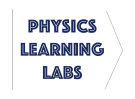
# -Graphics- Lab 0 - Introduction to Data Analysis

Welcome to Mathematica! Mathematica is the programming language we will be using in the laboratory to analyze data, create graphs, calculate error, visualize relationships between variables, and much more.

## Basics

### Input Output

Mathematica code is partitioned into “cells”. See the cells on the right?  
To execute code in Mathematica, navigate to any position on the desired input cell with your cursor and press Shift+Enter.

In the empty orange cell below, insert a random number. Then press Shift+Enter

Notice the input (In[1])and output (Out[1])?

** The cells also follow a hierarchy. To collapse a section, double click on one of the larger cell brackets on the right. Double click again to expand.

### Calculator

With ease, Mathematica can function as an ordinary calculator

Execute the input cells below (Shift+Enter)

```mathematica
1+2
```

```mathematica
3*10/2
```

```mathematica
(3^2+1)/2
```

Proper use of parenthesis is important. The expression above different than the expression below

Shift+Enter to execute

```mathematica
3^2+1/2
```

### Cell Types, Typesetting, Cell Tags

Orange cells indicate Input format (code). Yellow cells indicate text format, which are used to answer questions in Prelabs and Labs. Unless designed as an explicit question, most orange (code) cells are not editable. However, you can create a new cell at anytime by placing the cursor between two cells and typing.

The red square RGBColor[0.77, 0, 0] will always indicate an action item. This could be code to evaluate, a question to answer, or a physical step in the procedure. Some code items require you to create your own input.

Type your name in the text cell below

In answering questions in the text boxes, we will need to utilize some mathematical typesetting tools. An easy way to access these tools is to go to Palettes > Basic Math Assistant. Here we can implement greek letters, symbols, fractions, and more.

Use Basic Math Assistant to type the following equation:  . (Requires subscripts, fractions, and greek letters).

** A shortcut for inserting greek letters is to use “Esc”+“greek letter”+“Esc”. For fractions, you may use “CTRL”+“/”.

If you look to the left, you may see the gray “cell tags” on certain cells. These are used to reference questions for grading, equations, and figures. The above cell tag “Q5” indicates this is Question 5.

### Built-in Functions

To use elementary functions, such as Sin(x), e^x, ln(x), √3, we utilize Mathematica’s vast database of built-in functions. Functions will typically take the format f[x_], where f defines the function and x the argument. Native Mathematica functions always begin with a capital letter (and are thus case sensitive).

For example, we  may evaluate Cos(0) as

```mathematica
Cos[0]
```

Further examples:

```mathematica
Exp[3]
```

```mathematica
Sqrt[3]
```

In this example, Log[x] denotes the natural log, ln(x), while Log10[x] denotes log_10(x).

```mathematica
Log[2]
```

Notice that all of the above outputs are not in numerical form. To evaluate them to arbitrary decimal precision, we must further use the N[x_] function.

Example:

```mathematica
N[Exp[6]]
```

Calculate the numerical form of √3 and ln(2) below.

### Finding Functions and Syntax

To search for a built-in function within Mathematica, press F1 and enter your query. Selecting a specific function will reveal all its properties.

Search for the hyperbolic cosine function (cosh)

Search for the N[] function

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

Notice that N[] can take an additional optional argument, given by n (the digit of precision).

Using two arguments for the N[] function, numerically calculate e^6 with 8 digits of precision. Refer to the F1 documentation for help if needed.

In general, a function can take in an arbitrary number of arguments. Multiple arguments may be required or some may be optional (such as the optional n we saw for N[]). For Mathematica’s built-in functions, we have to know the proper “syntax” to use (i.e. the definition, order, and options of the arguments used in functions). In order to determine the appropriate syntax, we will often refer to the function documentation using F1.

** As a shortcut, you may always put a “?” in front of a function to display its documentation within the notebook itself. For example:

```mathematica
?Cos
```

## Defining Variables

To define a variable, we simply use “=”

For example, we assign the value of 5^2+3 to variable a

```mathematica
a=5^2 + 3
```

Once we execute the cell a = 5^2+3, we have stored our variable a as numerical value 28 within the computer. When we call upon a again, it “remembers”.

```mathematica
a
```

To avoid Mathematica internal errors, it may be necessary to clear the definition of a variable. This is done using the Clear[] function

First we see a takes the previous value of 28. After the Clear[] function, it is undefined, in which the output just returns back a

```mathematica
a
Clear[a]
a
```

** When making a definition of a variable, we can suppress the output by appending a semicolon. Take note of the difference between the two equivalent definitions.

Output is displayed

```mathematica
someinput = 1029378
```

Output is suppressed

```mathematica
someinput = 1029378;
```

## Lists

In future lab experiments, we will acquire large amounts of data in the form of lists or arrays. The native Mathematica function that represents a set of ordered elements is the List[] function.

For example, take the ordered list (1, 2, 3, 4, 5). To input such a list into Mathematica, we use the syntax {i_1, i_2, i_3,... , i_n}

Note the form of the list a

```mathematica
a = {1,2,3,4,5}
```

### Length of a List

Given our list a = {1,2,3,4,5}, we can find the length of this list, i.e. the total number of elements, with the function Length[]

```mathematica
Length[a]
```

### List Indexing

Let us start with a random collection of values, stored in the list-type variable named example.

```mathematica
example = {8,11,8,11,10,5,9,7,10,12,4,5,12,14,10,7,14,6,10,10,7,11,6,12,10,17,8,6,11,13,13,9,11,7,13,10,12,6,14,12,11,9,12,15,10,6,7,7,11,14,6,12,7,6,10,10,11,16,12,14,9,12,7,14,7,16,10,9,9,8,14,8,5,14,10,7,10,9,13,12,9,11,9,7,13,12,6,12,8,12,8,10,7,7,10,9,12,11,7,9};
```

To access any individual element of this list, we use two brackets, i.e. example[[i]] returns the i^th element of the list example.

Here we output the 5^th element of our list example. Check to make sure this matches expectation

```mathematica
example[[5]]
```

Sample the 7th element of the list example below

We can also have a list with two indices. For example

```mathematica
sample = {{3,2},{4,5},{7,1}};
```

Notice that sample is a single list of ordered pairs of numbers (a nested list).

Indexing nested lists is best seen by example.

Try to dissect what is happening below

```mathematica
sample[[1]]
```

```mathematica
sample[[2]]
```

```mathematica
sample[[2]][[1]]
```

```mathematica
sample[[2]][[2]]
```

Indexing the list sample, output the element with value 7

Recall that to find the total number of elements in a list, we utilize the Length[] function

## Plotting

### Continuous Variable

To plot an expression of a continuous variable (as opposed to lists of discrete values), we utilize the Plot[] function.

Let’s plot the function g(x) = x^2 from [-1,1]

```mathematica
Plot[x^2,{x,-1,1}]
```

Let’s note what we did here. As you can check in the F1 documentation for the Plot[] function, the first argument is the mathematical expression, which is in our case x^2. The next argument, which is enclosed in {} is the x range we would like to plot over, i.e. [-1,1].

If we want to label the axes, we include something called an option within the plot function. For example, to label the vertical axis as g(x) and the horizontal axis as x we add in the option AxesLabel{“ “,” “}

Here is how we would label the axes and store the plot as a variable gplot

```mathematica
gplot=Plot[x^2,{x,-1,1},AxesLabel->{"x","g(x)"}]
```

Note here that the AxesLabel option is followed by an arrow, which may be input on the keyboard as -> . Text is always encoded in parenthesis within Mathematica code.

Don’t worry too much about trying to remember the specific syntax for options like AxesLabel. You can always refer back to this lab (Lab 0) for the syntax or refer to the documentation. If you’ve developed a nice plot once, you can always go back and copy all its options, and change the specifics such as the labels and functions.

For the purposes of our experiments, the input code for most plots will be generated for you; however, it will be useful to understand their syntax.

### Discrete Variable

As mentioned, our experimental data is most often stored as lists of measured values. To plot data in this discrete form, we use the ListPlot[] function.

Below is an example list mydata composed of angles θ (°) and ranges R (m) of launched projectiles, stored in the form {{θ_1, R_1}, {θ_2, R_2}, {θ_3, R_3}, {θ_4, R_4}}

Load some example experimental results into mydata below

```mathematica
mydata = {{0,0},{10,0.22},{25,0.31},{50, 0.65}};
```

To plot mydata, we use the ListPlot[] function

```mathematica
ListPlot[mydata]
```

Notice the discrete values (i.e. our measurements) as opposed to the smooth continuous plot of x^2 we made. The ListPlot[] function takes the same options as the Plot[] function does. Hence, to add axes labels, we use the same syntax.

Create a discrete plot of mydata including appropriate axis labels ( θ (°),  R (m) ). Add in the option PlotStyle->Red to make the data points red. Lastly, store this plot as the variable mydataplot.

```mathematica
mydataplot=
```

(Hint: Refer to gplot to see the format for AxesLabels. Remember that AxesLabel and PlotStyle are both options to the function ListPlot. Multiple options must be separated by a comma.)

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).